## Setup

```mathematica
Get["FunKit`"]
```

Loading external dependencies...

TensorBases loaded

MaTeX loaded

Loading modules...

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

...DiRK loaded

...TRACY loaded

...COEN loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FInfo[].

```mathematica
fields= <|
"cField"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
bases={
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
};
diagramStyling=<|
"Styles"->{A->{Orange},c->{Black,Dashed}}
|>;
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;

SetTexStyles[cb->"\\bar{c}"];
SetGlobalSetup[Setup];
landauGauge=(#/.dressing[GammaN,{A,A},2,{__}]:>1/ξ//.ξ->0)&;
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{A,A},2,{a_,b_}]:>1,
dressing[GammaN,{c,cb},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},1,{p1_,p2_}]:>Zc[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{c,cb,A},1,{p1_,p2_,p3_}]:>ZccbA[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

dressing[S,{c,cb,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[S,{c,cb},1,{p1_,p2_}]->sp[p2,p2],
dressing[S,{A,A},1,{p1_,p2_}]->sp[p2,p2],

ZccbA[p1_,p2_]:>ZccbA[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA3[p1_,p2_]:>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA4[p1_,p2_,p3_]:>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[-p1-p2-p3,-p1-p2-p3]))],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*((ZA[1.02evP]-ZA[evP])/(0.02*evP))),
dressing[Rdot,{c,cb},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k((Zc[1.02*k]-Zc[k])/(0.02*k)))
}]&;

SetSymmetricDressing[GammaN,{A,A}]
PropParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p1,p1]->p^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos1,√(a_^2):>a}//DiagramSimplify;
SPParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p,p]->p^2,sp[l1,l1]->l1^2,√(a_^2):>a}//DiagramSimplify;
SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1-1<cos2<1&&-1<cos3<1;
```

```mathematica
Init[]:=Block[{Print},
Get["FunKit`"];

fields= <|
"cField"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
bases={
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
};
diagramStyling=<|
"Styles"->{A->{Orange},c->{Black,Dashed}}
|>;
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;

SetTexStyles[cb->"\\bar{c}"];
SetGlobalSetup[Setup];
landauGauge=(#/.dressing[GammaN,{A,A},2,{__}]:>1/ξ//.ξ->0)&;
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{A,A},2,{a_,b_}]:>1,
dressing[GammaN,{c,cb},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},1,{p1_,p2_}]:>Zc[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{c,cb,A},1,{p1_,p2_,p3_}]:>ZccbA[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

dressing[S,{c,cb,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[S,{c,cb},1,{p1_,p2_}]->sp[p2,p2],
dressing[S,{A,A},1,{p1_,p2_}]->sp[p2,p2],

ZccbA[p1_,p2_]:>ZccbA[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA3[p1_,p2_]:>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA4[p1_,p2_,p3_]:>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[-p1-p2-p3,-p1-p2-p3]))],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*((ZA[1.02evP]-ZA[evP])/(0.02*evP))),
dressing[Rdot,{c,cb},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k((Zc[1.02*k]-Zc[k])/(0.02*k)))
}]&;

SetSymmetricDressing[GammaN,{A,A}];
PropParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p1,p1]->p^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos1,√(a_^2):>a}//DiagramSimplify;
SPParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p,p]->p^2,sp[l1,l1]->l1^2,√(a_^2):>a}//DiagramSimplify;
SetNc[3];
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1-1<cos2<1&&-1<cos3<1;
];
```

## DSE

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


2 -Graphics-+12 -Graphics--3 -Graphics--4 -Graphics---Graphics-+12 -Graphics-

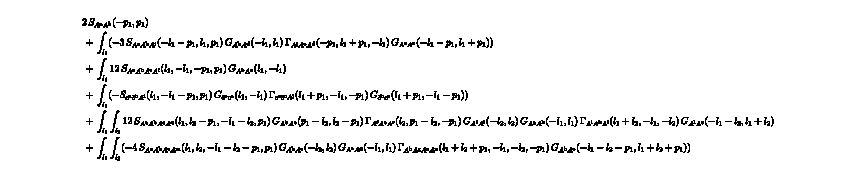

<|0-Loop→2 p^2,1-Loop→(12 (-1+cos1^2) gS (3 l1^4+6 cos1 l1^3 p+(8+cos1^2) l1^2 p^2+6 cos1 l1 p^3+3 p^4) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)])/(l1^2 (l1^2+2 cos1 l1 p+p^2)^2 Zc[l1] Zc[√(l1^2+2 cos1 l1 p+p^2)]),2-Loop→(216 gS^2 (sp[l1,l2]^3 (-5 p^2 sp[l2,l2]^2+(p^2-sp[l2,p1]) sp[l2,p1]^2+sp[l2,l2] (-8 p^4+12 p^2 sp[l2,p1]+sp[l2,p1]^2))+l1 sp[l1,l2] sp[l2,l2] (6 l1 (cos1 l1 p-2 sp[l2,p1]) (p^2-sp[l2,p1]) sp[l2,p1]+p sp[l2,l2]^2 (p (5 l1-2 cos1 p)+2 cos1 sp[l2,p1])+sp[l2,l2] (l1 p^3 (-4 cos1 l1+8 p+cos1^2 p)+p (-6 l1 p-cos1^2 l1 p+4 cos1 (l1^2+p^2)) sp[l2,p1]-(7 l1+4 cos1 p) sp[l2,p1]^2))+sp[l1,l2]^2 (-3 p^2 sp[l2,l2]^3+l1^2 (p^2-sp[l2,p1]) sp[l2,p1]^2+sp[l2,l2]^2 (-p^2 (5 l1^2+4 cos1 l1 p+5 p^2)+p (4 cos1 l1+7 p) sp[l2,p1]+sp[l2,p1]^2)+sp[l2,l2] (-8 l1^2 p^4+6 l1 p^2 (2 l1+cos1 p) sp[l2,p1]+(l1^2-6 cos1 l1 p+p^2) sp[l2,p1]^2-sp[l2,p1]^3))+l1^2 sp[l2,l2] (3 p^2 sp[l2,l2]^3+8 l1^2 sp[l2,p1]^2 (-p^2+sp[l2,p1])+sp[l2,l2]^2 (p^2 (5 l1^2-2 cos1 l1 p+5 p^2)+(2 cos1 l1-5 p) p sp[l2,p1]-3 sp[l2,p1]^2)+sp[l2,l2] ((8+cos1^2) l1^2 p^4-l1 p^2 ((8+cos1^2) l1-4 cos1 p) sp[l2,p1]-(5 l1^2+4 cos1 l1 p+5 p^2) sp[l2,p1]^2+5 sp[l2,p1]^3))) ZA3[√(2/3) √(l1^2+sp[l1,l2]+sp[l2,l2])] ZA3[√(2/3) √(p^2+sp[l2,l2]-sp[l2,p1])])/(l1^4 p^2 sp[l2,l2]^2 (l1^2+2 sp[l1,l2]+sp[l2,l2])^2 (p^2+sp[l2,l2]-2 sp[l2,p1])^2 Zc[l1] Zc[√sp[l2,l2]] Zc[√(l1^2+2 sp[l1,l2]+sp[l2,l2])] Zc[√(p^2+sp[l2,l2]-2 sp[l2,p1])])|>

```mathematica
DSEAA=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
DSEAAResult=Map[
(FormTrace[
F[TBGetProjector["AA",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
]//dressingRules//FORMSimplify//PropParam)&,
DSEAA]
```

```mathematica
DSEcbc=TakeDerivatives[MakeDSE[Setup,c[i1]],{cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEcbcResult=Map[
(FormTrace[
F[TBGetProjector["cbc",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
]//dressingRules//FORMSimplify//PropParam)&,
DSEcbc]
```

-Graphics-+-Graphics-

-Graphics-

<|0-Loop→p^2,1-Loop→(3 (-1+cos1^2) gS p^2 ZccbA[√(2/3) √(l1^2+cos1 l1 p+p^2)])/(l1^2 (l1^2+2 cos1 l1 p+p^2) ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[l1])|>

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[l1,p,p1,p2,p3];
```

```mathematica
DSEAcbc=TakeDerivatives[MakeDSE[Setup,c[i1]],{A[i3],cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEAcbcResult=Map[
(FormTrace[
F[TBGetProjector["Acbc",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEAcbc]
```

-Graphics---Graphics-+-Graphics-

-Graphics-

<|0-Loop→gS,1-Loop→(gS p (2 (cos2-2 cos1^2 cos2+cos1 (-1+2 cos2^2)) l1^3+2 (-3+cos1^2-2 cos1^3 cos2+6 cos2^2+cos1 cos2 (5+2 cos2^2)) l1^2 p+(-5 cos1-7 cos2+10 cos1^2 cos2+24 cos1 cos2^2+14 cos2^3) l1 p^2+3 (-1+2 cos1 cos2+2 cos2^2) p^3) ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZccbA[√(2/3) √(l1^2+cos2 l1 p+p^2)])/(2 l1^2 (l1^2+2 cos2 l1 p+p^2) (l1^2+2 (cos1+cos2) l1 p+p^2)^2 ZA[√(l1^2+2 cos2 l1 p+p^2)] Zc[l1] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])|>

6 -Graphics--3 -Graphics--24 -Graphics-+6 -Graphics-+12 -Graphics-+24 -Graphics--2 -Graphics--24 -Graphics--24 -Graphics-

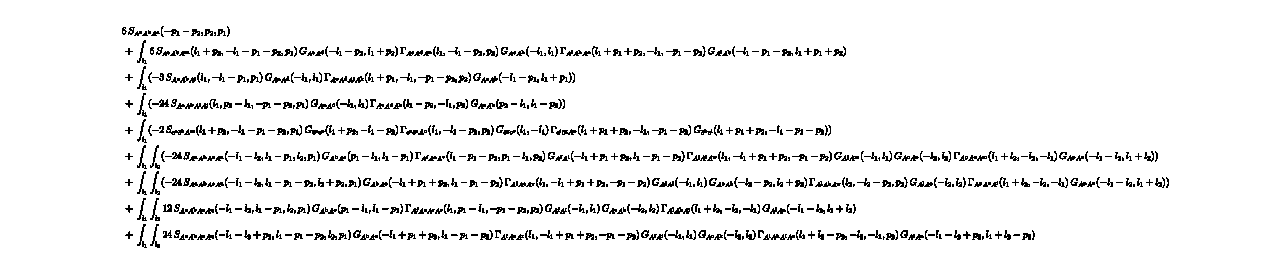

$Aborted

```mathematica
DSEA3=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i3],A[i2]},"Symmetries"->symmetryP3]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
DSEA3Result=Map[
(FormTrace[
F[TBGetProjector["AAAClassTrans",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEA3]
```

## 4Point

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
```

```mathematica
DSEA4=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i4],A[i3],A[i2]},"Symmetries"->symmetryP4]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
```

24 -Graphics--36 -Graphics-+18 -Graphics-+72 -Graphics-+36 -Graphics--18 -Graphics--36 -Graphics--36 -Graphics--72 -Graphics--72 -Graphics--72 -Graphics--6 -Graphics-+72 -Graphics-+144 -Graphics-+24 -Graphics-

-Graphics-

## fRG

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


--Graphics-/2-2 -Graphics-+-Graphics-

-Graphics-

((7-cos1^2) (-RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] (-dtZA[(1+k^6)^(1/6)]+(50 k^6 (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)]))/(1+k^6))) ZA4[(√(l1^2+p^2))/(√2)])/(l1^4 Zc[l1]^2)-(4 (-1+cos1^2) (3 l1^4+6 cos1 l1^3 p+(8+cos1^2) l1^2 p^2+6 cos1 l1 p^3+3 p^4) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2)/((1+k^6) l1^4 (l1^2+2 cos1 l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])-(2 (-1+cos1^2) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)]^2)/(l1^2 (l1^2-2 cos1 l1 p+p^2) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)])

```mathematica
fRGAA=TakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
traceExprAA=F[TBGetProjector["AA",1,{i1,i2}/.fRGAA["1-Loop"]["ExternalIndices"]],(fRGAA["1-Loop"]["Expression"]/.MakeDiagrammaticRules[]//landauGauge)];
FlowAA=FormTrace[traceExprAA]//dressingRules//FORMSimplify//PropParam
```

```mathematica
fRGcbc=TakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
traceExprcbc=F[TBGetProjector["cbc",1,{i1,i2}/.fRGcbc["1-Loop"]["ExternalIndices"]],(fRGcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[]//landauGauge)];
Flowcbc=FormTrace[traceExprcbc]//dressingRules//FORMSimplify//PropParam
```

--Graphics---Graphics-

-Graphics-

(3 (-1+cos1^2) p^2 (-((l1^2+2 cos1 l1 p+p^2) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)])/(ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[l1]^2)-((l1^2+2 cos1 l1 p+p^2) RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)])))/((1+k^6) ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[l1]^2)+(l1^2 (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])))/(ZA[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])) ZccbA[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2)/(l1^4 (l1^2+2 cos1 l1 p+p^2)^2)

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[l1,p,p1,p2,p3];
```

```mathematica
fRGAcbc=TakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
projectorAcbc=TBGetProjector["Acbc",1,{i1,i2,i3}/.fRGAcbc["1-Loop"]["ExternalIndices"]];
traceExprAcbc=F[projectorAcbc,(fRGAcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[]//landauGauge)];FlowAcbc=FormTrace[traceExprAcbc,SP3FormRule,SP3FormRule]//dressingRules//FORMSimplify[#,SP3FormRule,SP3FormRule]&//SPParam
```

--Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics---Graphics-

-Graphics-

((cos1+2 cos2) p ((-1+2 cos1 cos2+2 cos2^2) l1+(2 cos1+cos2) p) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2+cos2 l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (-cos1+cos2) l1 p+p^2)])/(2 l1^2 (l1^2-2 cos1 l1 p+p^2) (l1^2+2 cos2 l1 p+p^2)^2 ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] Zc[√(l1^2+2 cos2 l1 p+p^2)])+((-1/(1+k^6)p (-2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2)-2 (3+2 cos1^3 cos2-2 cos2^2+6 cos1^2 (-1+cos2^2)+cos1 cos2 (-7+4 cos2^2)) l1^2 p+(14 cos1^3-2 cos2+18 cos1^2 cos2+cos1 (-7+4 cos2^2)) l1 p^2+3 (-1+2 cos1^2+2 cos1 cos2) (p^2)^(3/2)) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA[√(l1^2+2 (cos1+cos2) l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]+(l1^2 Zc[l1] (-((2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2) p+2 (3+2 cos1^3 cos2-2 cos2^2+6 cos1^2 (-1+cos2^2)+cos1 cos2 (-7+4 cos2^2)) l1^2 p^2-3 (-1+2 cos1^2+2 cos1 cos2) p^4+(-14 cos1^3+2 cos2-18 cos1^2 cos2+cos1 (7-4 cos2^2)) l1 (p^2)^(3/2)) dtZc[k] RB[k^2,l1^2+2 (cos1+cos2) l1 p+p^2] ZA[l1]^2 ZA[√(l1^2+2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])+p (-2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2)-2 (3+2 cos1^3 cos2-2 cos2^2+6 cos1^2 (-1+cos2^2)+cos1 cos2 (-7+4 cos2^2)) l1^2 p+(14 cos1^3-2 cos2+18 cos1^2 cos2+cos1 (-7+4 cos2^2)) l1 p^2+3 (-1+2 cos1^2+2 cos1 cos2) (p^2)^(3/2)) ZA[l1]^2 ZA[√(l1^2+2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] (RBdot[k^2,l1^2+2 (cos1+cos2) l1 p+p^2] Zc[k]-50 RB[k^2,l1^2+2 (cos1+cos2) l1 p+p^2] (Zc[k]-Zc[(51 k)/50])) Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]+(cos1+2 cos2) p ((-1+2 cos1 cos2+2 cos2^2) l1+(-cos1+cos2) p) (l1^2+2 cos1 l1 p+p^2) RBdot[k^2,l1^2] ZA[√(l1^2+2 (cos1+cos2) l1 p+p^2)]^2 Zc[k] Zc[l1] Zc[√(l1^2+2 cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2+cos1 l1 p+p^2)]+(cos1+2 cos2) p ((-1+2 cos1 cos2+2 cos2^2) l1+(-cos1+cos2) p) (l1^2+2 cos1 l1 p+p^2) RB[k^2,l1^2] ZA[√(l1^2+2 (cos1+cos2) l1 p+p^2)]^2 (dtZc[k]+50 (-Zc[k]+Zc[(51 k)/50])) Zc[l1] Zc[√(l1^2+2 cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2+cos1 l1 p+p^2)]))/((l1^2+2 (cos1+cos2) l1 p+p^2) ZA[l1]^2 ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])) ZccbA[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)])/(2 l1^4 (l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2) ZA[√(l1^2+2 (cos1+cos2) l1 p+p^2)]^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])+(ZccbA[√(2/3) √(l1^2-cos2 l1 p+p^2)] ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)] ((l1^2-2 (cos1+cos2) l1 p+p^2) (-2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2) p-2 (-3+2 cos1^3 cos2+2 cos2^2+cos1 cos2 (-3+4 cos2^2)+cos1^2 (1+6 cos2^2)) l1^2 p^2+3 (1+2 cos1 cos2) p^4+(-2 cos2+10 cos1^2 cos2+cos1 (5-4 cos2^2)) l1 (p^2)^(3/2)) ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (cos1-cos2) l1 p+p^2)]-1/2 (-1+2 cos1 cos2+2 cos2^2) (2 cos1 l1+4 cos2 l1-3 p) p (l1^2+2 cos1 l1 p+p^2)^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (cos1+2 cos2) l1 p+p^2)])+RB[k^2,l1^2] (-25 k^6 (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)]) (2 (l1^2-2 (cos1+cos2) l1 p+p^2) (-2 (-cos1+2 cos2 (-1+cos1^2+3 cos1 cos2+2 cos2^2)) (l1^2)^(3/2) p-2 (-3+2 cos1^3 cos2+2 cos2^2+cos1 cos2 (-3+4 cos2^2)+cos1^2 (1+6 cos2^2)) l1^2 p^2+3 (1+2 cos1 cos2) p^4+(5 cos1-2 cos2 (1-5 cos1^2+2 cos1 cos2)) l1 (p^2)^(3/2)) ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (cos1-cos2) l1 p+p^2)]-(-1+2 cos1 cos2+2 cos2^2) (2 cos1 l1+4 cos2 l1-3 p) p (l1^2+2 cos1 l1 p+p^2)^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (cos1+2 cos2) l1 p+p^2)])+(1+k^6) dtZA[(1+k^6)^(1/6)] ((l1^2-2 (cos1+cos2) l1 p+p^2) (-2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2) p-2 (-3+2 cos1^3 cos2+2 cos2^2+cos1 cos2 (-3+4 cos2^2)+cos1^2 (1+6 cos2^2)) l1^2 p^2+3 (1+2 cos1 cos2) p^4+(-2 cos2+10 cos1^2 cos2+cos1 (5-4 cos2^2)) l1 (p^2)^(3/2)) ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (cos1-cos2) l1 p+p^2)]-1/2 (-1+2 cos1 cos2+2 cos2^2) (2 cos1 l1+4 cos2 l1-3 p) p (l1^2+2 cos1 l1 p+p^2)^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (cos1+2 cos2) l1 p+p^2)]))))/(2 (1+k^6) l1^4 (l1^2+2 cos1 l1 p+p^2)^2 (l1^2-2 cos2 l1 p+p^2) (l1^2-2 (cos1+cos2) l1 p+p^2) ZA[√(l1^2-2 cos2 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)] Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])

```mathematica
fRGA3=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
projectorA3=TBGetProjector["AAAClassTrans",1,{i1,i2,i3}/.fRGA3["1-Loop"]["ExternalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//Simplify;
traceExprA3=F[projectorA3,(fRGA3["1-Loop"]["Expression"]/.MakeDiagrammaticRules[]//landauGauge)];
FlowA3=FormTrace[traceExprA3,{},SP3FormRule]//dressingRules//FORMSimplify[#,{},SP3FormRule]&//SPParam
```

3 -Graphics--6 -Graphics--3 -Graphics-

-Graphics-

(ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ((1+k^6) (24 (2 cos1^3+3 cos1^2 cos2-3 cos1 cos2^2-2 cos2^3) (l1^2)^(7/2)+4 (2 cos1 (-36+97 cos1^2+26 cos1^4)-cos2 (36-130 cos1^4-4 cos1^3 cos2+50 cos2^2+4 cos2^4+cos1 cos2 (3+58 cos2^2)+cos1^2 (-291+124 cos2^2))) (l1^2)^(5/2) p^2+2 (224 cos1^5+560 cos1^4 cos2+16 cos1^3 (60+17 cos2^2)-8 cos1^2 cos2 (-180+19 cos2^2)-cos2 (241+64 cos2^2)+cos1 (-482+352 cos2^2-88 cos2^4)) (l1^2)^(3/2) p^4+231 (4 cos1^3-cos2+6 cos1^2 cos2+2 cos1 (-1+cos2^2)) l1 p^6-2 (186-163 cos1^2-2 cos1^4 (311+8 cos1^2)-cos1 (163+1244 cos1^2+48 cos1^4) cos2+2 cos2^2 (-14-10 cos1^4+20 cos1^3 cos2+60 cos2^2+cos1^2 (-109+18 cos2^2)+cos1 (202 cos2+4 cos2^3))) l1^4 (p^2)^(3/2)+99 (-1+2 cos1^2+2 cos1 cos2) (p^2)^(7/2)+3 l1^2 p (4 (-6+16 cos1^4+32 cos1^3 cos2+2 cos2^2-8 cos2^4+cos1^2 (11-12 cos2^2)+cos1 (11 cos2-28 cos2^3)) l1^4+(418 cos1^4+836 cos1^3 cos2-6 (21+4 cos2^2)+cos1 cos2 (51+16 cos2^2)+cos1^2 (51+434 cos2^2)) p^4)) (dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]-3 (1+k^6) p (l1^2+2 (cos1+cos2) l1 p+p^2)^2 ((-54+53 cos1^2-4 cos1 cos2-4 cos2^2) l1^2+cos1 (-54+53 cos1^2-4 cos1 cos2-4 cos2^2) l1 p+33 (-1+cos1^2) p^2) (dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]) ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)]) ((24 (2 cos1^3+3 cos1^2 cos2-3 cos1 cos2^2-2 cos2^3) (l1^2)^(7/2)+4 (2 cos1 (-36+97 cos1^2+26 cos1^4)-cos2 (36-130 cos1^4-4 cos1^3 cos2+50 cos2^2+4 cos2^4+cos1 cos2 (3+58 cos2^2)+cos1^2 (-291+124 cos2^2))) (l1^2)^(5/2) p^2+2 (224 cos1^5+560 cos1^4 cos2+16 cos1^3 (60+17 cos2^2)-8 cos1^2 cos2 (-180+19 cos2^2)-cos2 (241+64 cos2^2)+cos1 (-482+352 cos2^2-88 cos2^4)) (l1^2)^(3/2) p^4+231 (4 cos1^3-cos2+6 cos1^2 cos2+2 cos1 (-1+cos2^2)) l1 p^6-2 (186-163 cos1^2-2 cos1^4 (311+8 cos1^2)-cos1 (163+1244 cos1^2+48 cos1^4) cos2+2 cos2^2 (-14-10 cos1^4+20 cos1^3 cos2+60 cos2^2+cos1^2 (-109+18 cos2^2)+cos1 (202 cos2+4 cos2^3))) l1^4 (p^2)^(3/2)+99 (-1+2 cos1^2+2 cos1 cos2) (p^2)^(7/2)+3 l1^2 p (4 (-6+16 cos1^4+32 cos1^3 cos2+2 cos2^2-8 cos2^4+cos1^2 (11-12 cos2^2)+cos1 (11 cos2-28 cos2^3)) l1^4+(418 cos1^4+836 cos1^3 cos2-6 (21+4 cos2^2)+cos1 cos2 (51+16 cos2^2)+cos1^2 (51+434 cos2^2)) p^4)) ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]-3 p (l1^2+2 (cos1+cos2) l1 p+p^2)^2 ((-54+53 cos1^2-4 cos1 cos2-4 cos2^2) l1^2+cos1 (-54+53 cos1^2-4 cos1 cos2-4 cos2^2) l1 p+33 (-1+cos1^2) p^2) ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])))/(11 (1+k^6) l1^4 √(p^2) (l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])+(((4 cos1^3+6 cos1^2 cos2-6 cos1 cos2^2-4 cos2^3) l1-(-6+11 cos1^2+11 cos1 cos2+2 cos2^2) p) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (2 cos1+cos2) l1 p+p^2)])/(11 l1^2 √(p^2) (l1^2-2 cos1 l1 p+p^2) (l1^2-2 (cos1+cos2) l1 p+p^2) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)])

## 4Point

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
SP4FormRule=MakeSPFormRule[l1,p,p1,p2,p3,p4];
```

```mathematica
fRGA4=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3],A[i4]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
projectorA4=TBGetProjector["AAAAClassTrans",1,{i1,i2,i3,i4}/.fRGA4["1-Loop"]["ExternalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&//Simplify;
traceExprA4=F[projectorA4,(fRGA4["1-Loop"]["Expression"]/.MakeDiagrammaticRules[]//landauGauge)];
FlowA4=FormTrace[traceExprA4,SP4FormRule,SP4FormRule]//.dressingRules//FORMSimplify[#,SP4FormRule,SP4FormRule]&//SPParam
```

3 -Graphics--12 -Graphics--6 -Graphics--24 -Graphics-+12 -Graphics-

-Graphics-